```mathematica
SetDirectory["/home/andrzej/Documents/Uczelnia/Anizotropie/FunctionalIntegrator"];
zNormalization=0;
Get["../FunctionalRenormalization/FixedPoint.wl"]
SelectRegulator["smooth"]
```

```mathematica
Protect[rho, V, Zs, Zp, t, η, Z];
```

```mathematica
ReadFile[name_]:=Block[{breaks,data ,ends, ts, etas, Zets, actionStarts, actionEnds, indices, actions, ParseAction,AssignData},
data = Import[name];
ends = Flatten[Position[data,{}]];
{ts, etas, Zets} = Transpose[data[[2;;ends[[1]]-1]]];
actionStarts = Flatten[Position[data,{"Rho","V","Zs","Zp"}]+1];
actionEnds = ends[[2;;-1]]-1;
indices = Transpose[{actionStarts,actionEnds}];
ParseAction[startend_]:=Block[{dat,headers,action},
dat = Transpose[data[[startend[[1]];;startend[[2]]]]];
headers = {rho,V,Zs,Zp};

action = Association[Map[#[[1]]->#[[2]]&,Transpose[{headers,dat}]]];
Return[action];
];

actions = Map[ParseAction, indices];
AssignData[i_] := Block[{a},
a = actions[[i]];
a[t] = ts[[i]];
a[η] = etas[[i]];
a[Z] = Zets[[i]];
actions[[i]] = a;
];
Map[AssignData,Range[Length[actions]]];
Return[actions];
]
```

```mathematica
MakeGuess[action_]:=Block[{gv,gzs,gzp,gη},
gv = Map[v[#-1]->action[V][[#]]&,Range[Length[action[V]]]];
gzs = Map[zs[#-1]->action[Zs][[#]]&,Range[Length[action[V]]]];
gzp = Map[zp[#-1]->action[Zp][[#]]&,Range[Length[action[V]]]];
gη = {η->action[η]};
Return[Join[gv,gzs,gzp,gη]];
]
```

```mathematica
l = ReadFile["low_delta2.csv"];
d = ReadFile["low_delta.csv"];
a = ReadFile["low_delta3.csv"];
```

```mathematica
a[[1]][η]
```

0

```mathematica
filename[n_,a_]:= "results/flow_N="<>ToString[NumberForm[N[n],{2,1}]]<>"_a="<>ToString[a]<>".csv"
```

```mathematica
ns =1+0.2 Range[0,5];
as = {2};
```

```mathematica
args = Tuples[{ns,as}];
```

```mathematica
fullData = Association[Map[#->ReadFile[filename[#[[1]],#[[2]]]]&,args]];
```

```mathematica
ExtractV[action_]:=action[t]->Transpose[{action[rho],action[V]}]
ExtractZs[action_]:=action[t]->Transpose[{action[rho],action[Zs]}]
ExtractZp[action_]:=action[t]->Transpose[{action[rho],action[Zp]}]
Extractη[action_]:=action[t]->action[η]
```

```mathematica
Association[Map[Extractη,fullData[{2.,2}]]]
```

<|0→0,0.2→0.000278071,0.4→0.000640929,0.6→0.00141313,0.8→0.00301109,1→0.00618526,1.19995→0.0121458,1.3997→0.0225469,1.59905→0.0391206,1.79765→0.0628279,1.9954→0.0929505,2.1925→0.126942,2.3895→0.161474,2.5869→0.193767,2.7849→0.222211,2.98345→0.246255,3.1825→0.266033,3.3819→0.282008,3.5815→0.294761,3.78125→0.30487,3.9811→0.312838,4.18105→0.319079,4.381→0.323918,4.581→0.327611,4.781→0.330349,4.981→0.332285,5.181→0.333535,5.381→0.334195,5.581→0.334347,5.781→0.334064,5.981→0.333416,6.181→0.332467,6.381→0.331281,6.581→0.329919,6.781→0.328437,6.981→0.326887,7.181→0.325312,7.381→0.323749,7.581→0.322225,7.781→0.32076,7.981→0.319367,8.181→0.31805,8.381→0.316808,8.581→0.315636,8.781→0.314523,8.981→0.313457,9.181→0.312423,9.381→0.311403,9.581→0.310378,9.781→0.30933,9.981→0.308234,10.181→0.307069,10.381→0.305808,10.581→0.304423,10.781→0.302884,10.981→0.301155,11.181→0.299198,11.381→0.296967,11.581→0.294413,11.781→0.291478,11.981→0.288095,12.181→0.284189,12.3809→0.279674,12.5809→0.274454|>

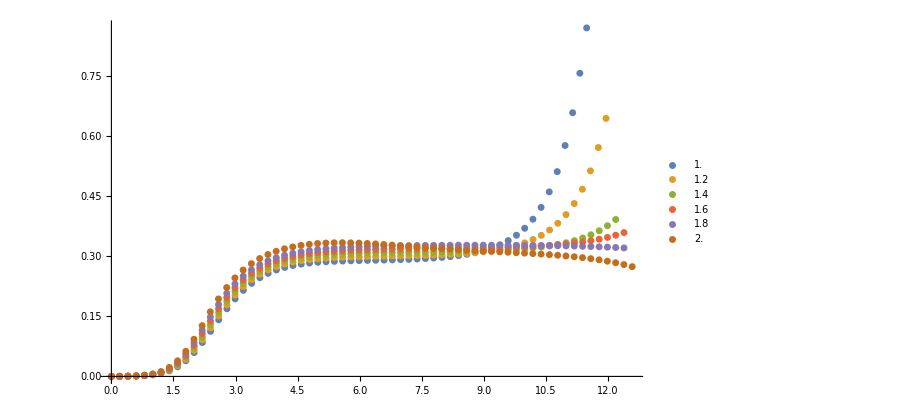

```mathematica
ListPlot[Table[Association[Map[Extractη,fullData[{ns[[i]],2}]]],{i,1,6}], PlotLegends->ns]
```

```mathematica
ListPlot[Values[Association[Map[ExtractZs,fullData[2.5]]]][[1;;-1;;5]],PlotRange->{0,2}]
```

```mathematica
fullData[[1;;-1;;5]]
```

<|{1.,2}→{<|rho→{0,0.0117333,0.0234666,0.0351998,0.0469331,0.0586664,0.0703997,0.0821329,0.0938662,0.105599,0.117333,0.129066,0.140799,0.152533,0.164266,0.175999,0.187732,0.199466,0.211199,0.222932,0.234666,0.246399,0.258132,0.269865,0.281599,0.293332,0.305065,146,2.02986,2.04159,2.05332,2.06506,2.07679,2.08852,2.10026,2.11199,2.12372,2.13546,2.14719,2.15892,2.17066,2.18239,2.19412,2.20586,2.21759,2.22932,2.24106,2.25279,2.26452,2.27626,2.28799,2.29972,2.31146,2.32319,2.33492},5,Z→1|>,57,<|1|>},1|>
 |  |  |  |

{0,1,1.9962,2.9853,3.98305,4.98295,5.98295,6.98295,7.98295,8.98295,9.98295,10.9829,11.9829}

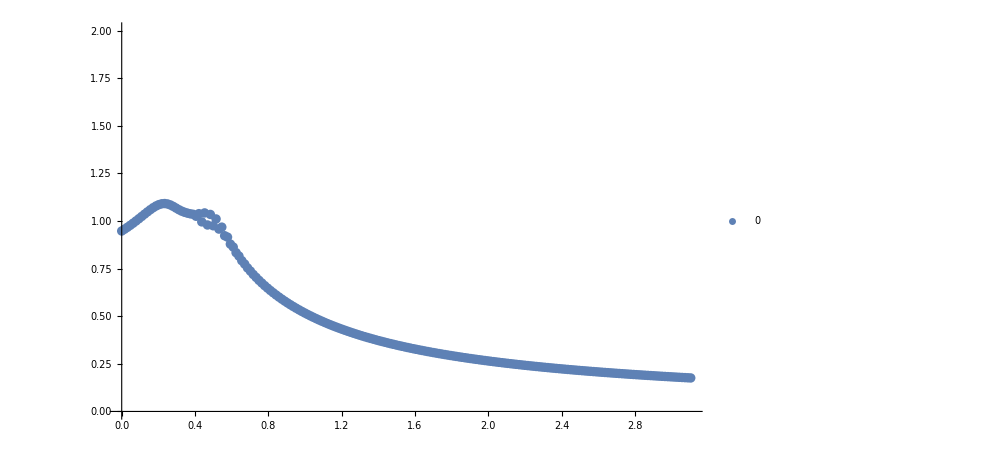

```mathematica
ListPlot[Values[Association[Map[ExtractZs,fullData[{1.8,2}]]]][[-5]],PlotRange->{0,2},PlotLegends->Map[#[t]&,fullData[{1.8,2}][[1;;-1;;5]]]]
```

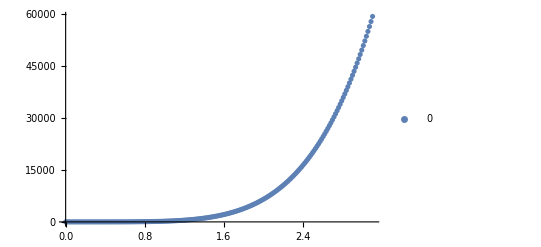

```mathematica
ListPlot[Values[Association[Map[ExtractV,fullData[{1.8,2}]]]][[-1]],PlotRange->All,PlotLegends->Map[#[t]&,fullData[{1.8,2}][[1;;-1;;5]]]]
```

```mathematica
%113[[-30]]
```

5.69983

```mathematica
Length[v18]
```

120

```mathematica
Length[Range[2,Length[v]-3]]
```

116

```mathematica
a3d[[1]][rho]
```

{0,0.0666667,0.133333,0.2,0.266667,0.333333,0.4,0.466667,0.533333,0.6,0.666667,0.733333,0.8,0.866667,0.933333,1,1.06667,1.13333,1.2,1.26667,1.33333,1.4,1.46667,1.53333,1.6,1.66667,1.73333,1.8,1.86667,1.93333,2,2.06667,2.13333,2.2,2.26667,2.33333,2.4,2.46667,2.53333,2.6,2.66667,2.73333,2.8,2.86667,2.93333,3,3.06667,3.13333,3.2,3.26667,3.33333,3.4,3.46667,3.53333,3.6,3.66667,3.73333,3.8,3.86667,3.93333}

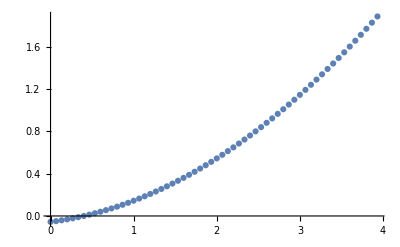

```mathematica
ListPlot[Transpose[{a3d[[1]][rho],v}]]
```

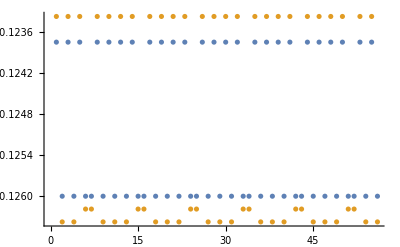

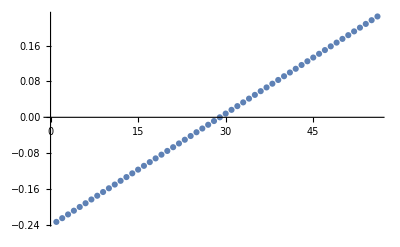

```mathematica
v = a3d[[1]][Zp];
step =a3d[[1]][rho][[2]];
vder = -(1/12v[[1;;-5]]  - 2/3v[[2;;-4]]+ 2/3v[[4;;-2]]−1/12v[[5;;-1]])/step;
vder2 = (−1/12v[[1;;-5]]  + 4/3v[[2;;-4]]−5/2v[[3;;-3]]+ 4/3v[[4;;-2]]−1/12v[[5;;-1]])/step^2;
vder3 = (v[[2;;-4]]−2v[[3;;-3]]+ v[[4;;-2]])/step^2;
ListPlot[{vder3, vder2},PlotRange->All]
ListPlot[{vder},PlotRange->All]
```

```mathematica
Simplify[u(x-k0) +V*x*x/.k0->k(1+k*V/u)]/.x->0
```

-k (u+k V)

```mathematica
vData = Association[Map[ExtractV,fullData[1.7999999999999998][[1;;-1;;15]]]];
```

```mathematica
zsData = Association[Map[ExtractZs,fullData[1.7999999999999998][[1;;-1;;15]]]];
```

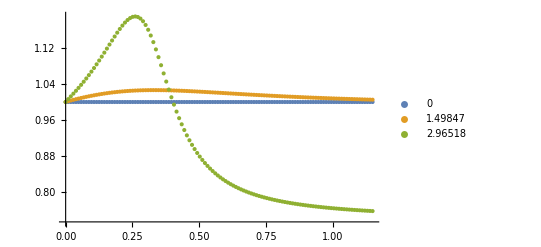

```mathematica
ListPlot[Values[zsData],PlotLegends->Keys[zsData]]
```

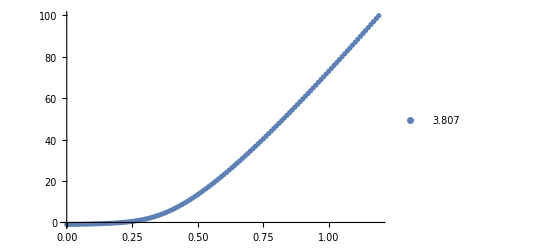

```mathematica
zsData = Association[Map[ExtractV,fullData[1.7999999999999998][[-1;;-1]]]];
ListPlot[Values[zsData],PlotLegends->Keys[zsData]]
```

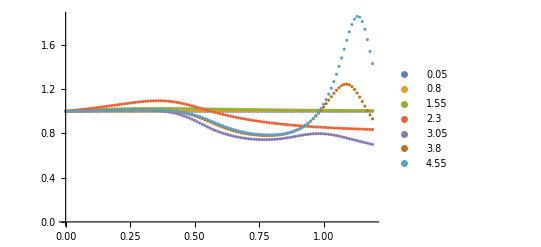

```mathematica
zsData = Association[Map[ExtractZs,fullData[2.][[1;;-1;;15]]]];
ListPlot[Values[zsData],PlotLegends->Keys[zsData],PlotRange->All]
```

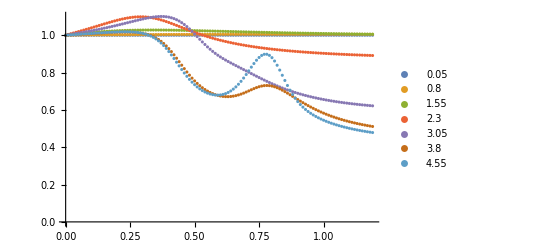

```mathematica
zsData = Association[Map[ExtractZs,fullData[1.9][[1;;-1;;15]]]];
ListPlot[Values[zsData],PlotLegends->Keys[zsData]]
```

```mathematica
Remove[etaData]
```

```mathematica
etaData[data_] := Map[{#[t],#[η]}&,data];
```

```mathematica
selectDims = 1.4+0.1Range[7];
```

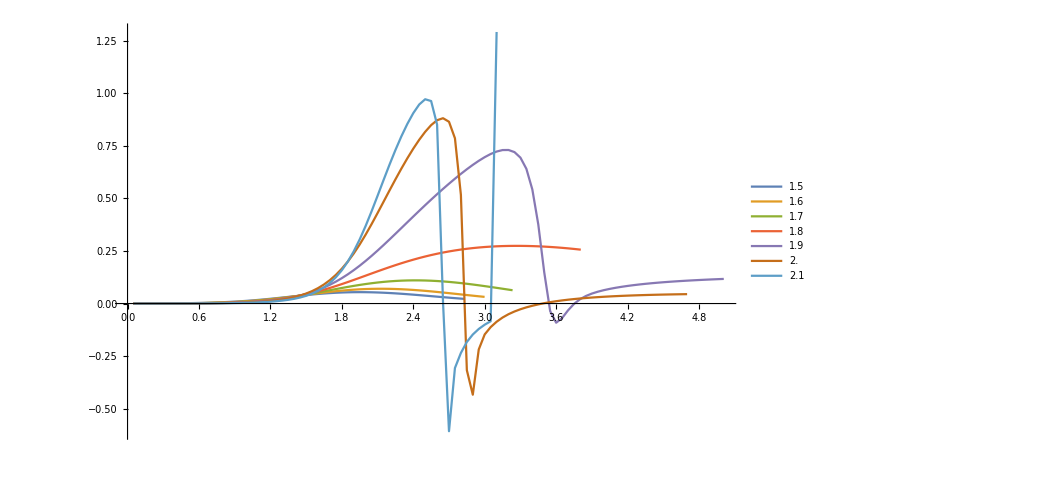

```mathematica
ListLinePlot[Map[etaData[fullData[#]]&,selectDims], PlotLegends->selectDims,PlotRange->All]
```